## Config

Source folder for JPG files

```mathematica
jpgFileNames=FileNames["*.jpg"|"*.JPG","/media/superraid/images/images/",∞];
```

Number of images found:

```mathematica
Length[jpgFileNames]
```

2881

Folder for local data storage:

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"dataStorage"}]
```

/home/malte/dev/imStat/dataStorage

```mathematica
CreateDirectory[dataDir]
```

CreateDirectory::filex: "/home/malte/dev/imStat/dataStorage/" already exists.

/home/malte/dev/imStat/dataStorage

## Retrieve mini JPG files and basic data

Compute data file name from original path:

```mathematica
storageFile[path_]:=FileNameJoin[{dataDir,ToString[Hash[path]]<>".dst"}];
```

Fetch original image and save data into data file:

```mathematica
createData[path_]/;FileExistsQ[storageFile[path]]=Null;
```

```mathematica
createData[path_]:=Module[{img,dimensions,smallImg,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model},
img=Import[path];
dimensions=ImageDimensions[img];
smallImg=ImageResize[img,{300}];
{aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model}=Import[path,{{"Aperture","BitDepth","CameraTopOrientation","ColorSpace","Date","Exposure","FocalLength","ImageSize","ISOSpeed","Manufacturer","Model"}}];
Put[{smallImg,dimensions,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model},storageFile[path]];
]
```

Fetch data in order of preference {memory, data file, source image}:

```mathematica
getData[path_]/;FileExistsQ[storageFile[path]]:=getData[path]=Get[storageFile[path]]
getData[path_]:=(createData[path];getData[path])
```

```mathematica
getData[path_,"Date"]:=getData[path][[7]]
```

## Test image data retrieval

```mathematica
iName=jpgFileNames[[7]]
```

/media/superraid/images/images/2007/2007-12-26--15.26.07/IMG_5910_autowb.jpg

First fetch takes long:

```mathematica
AbsoluteTiming[getData[iName];]
```

ICCObject::iccinv: -- Message text not found -- (ICCObject[])

{4.11746,Null}

Fetching from memory:

```mathematica
AbsoluteTiming[getData[iName];]
```

{0.00004,Null}

```mathematica
Quit
```

```mathematica
iName=jpgFileNames[[7]];
```

Fetching from local data file:

```mathematica
AbsoluteTiming[getData[iName];]
```

ICCObject::iccinv: -- Message text not found -- (ICCObject[])

{0.366232,Null}

Fetching from memory:

```mathematica
AbsoluteTiming[getData[iName];]
```

{0.000041,Null}

## Retrieve image data

```mathematica
Monitor[
ParallelDo[createData[jpgFileNames[[i]]],{i,Length[jpgFileNames]}],
Refresh[
ProgressIndicator[Length@FileNames["*",dataDir],{0,Length[jpgFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
]
```

## Number of images taken

```mathematica
Length[jpgFileNames]
```

2881

## Images taken over time

```mathematica
imageDates=Monitor[
Table[getData[jpgFileNames[[i]],"Date"],{i,Length[jpgFileNames]/2}],
Refresh[
ProgressIndicator[i,{0,Length[jpgFileNames]/2}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

ICCObject::iccinv: -- Message text not found -- (ICCObject[])

General::stop: Further output of ICCObject :: iccinv will be suppressed during this calculation.

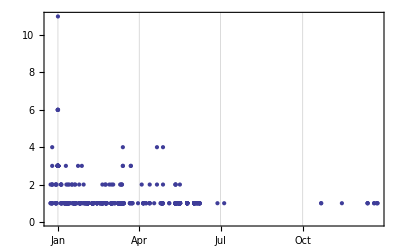

```mathematica
DateListPlot@Tally[Cases[imageDates,{y_,mo_,d_,h_,mi_,s_}]]
```

## ...